```mathematica
(** ERROR ANALYSIS FOR NCC AND BBC RELATIVE TO ECC, USED TO ESTIMATE THE FNR OF THE PR MONITOR **)
```

```mathematica
(* these charts show how mean squared error (MSE) of NCC (blue) and BBC (yellow) changes with quantity of information,  over for different window sizes (d) *)
```

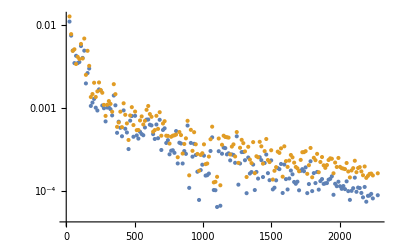
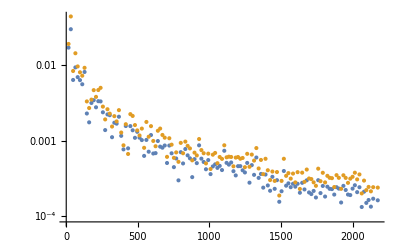
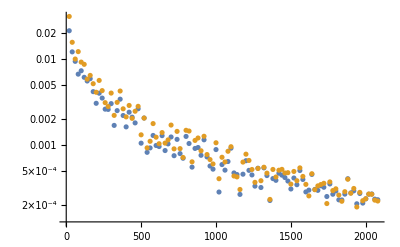
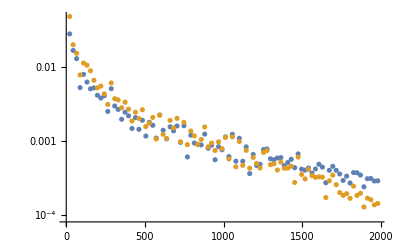
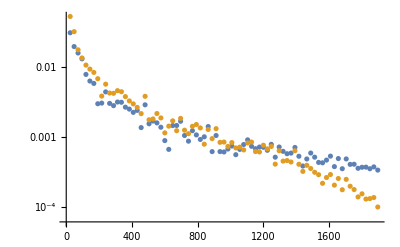
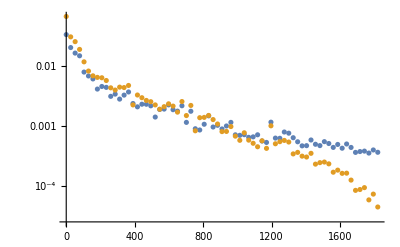
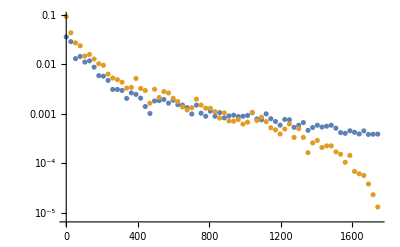
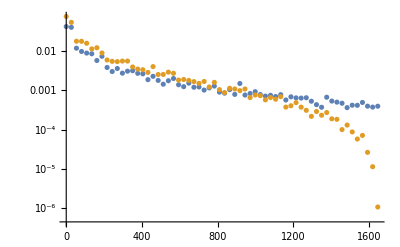
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(Clear[data];data = getFnrMSQPairsWithBins[ (* sessions *) {4,5,6,7},(*samples per subset size*)40, (*win size *) #, (* bin width: *)Round[countFromFiles[ "FNcount", allMonFilenames[{4,5,6,7},(*monwin*) #]]/(*number of bins we want*)50]];
ListLogPlot[{data[[All,{1,3}]], data[[All,{1,4}]]}, PlotRange->All])&/@ Range[2,30]
```

```mathematica
data = With[{reslist = getPrFNRPointEstResidualsWithH1ct[{4,5,6,7},(*samples per subset size*) 40, (*winsize*)#]}, {{#,Mean@(reslist[[All,2]]^2)},{#,Mean@(reslist[[All,3]]^2)}}]& /@ Range[2,2];
```

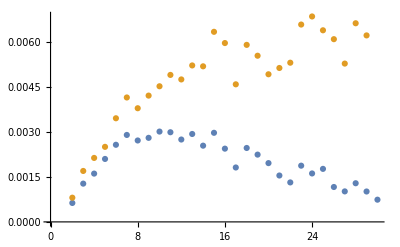

```mathematica
(*** DEPENDENCY OF MSE ON WINDOW SIZE (d) 
-- aggregation of the above charts: two points per chart
***) 
ListPlot@Transpose@data
```

```mathematica
(* values: *) 
dataPrMseByD = {{{2,0.0006321193204417888},{2,0.0008088844409567721}},{{3,0.001278179176567287},{3,0.001701462971482259}},{{4,0.001613261367736009},{4,0.0021367466699191433}},{{5,0.0021028411524843236},{5,0.002506901188586144}},{{6,0.0025759659825148186},{6,0.0034616158149913976}},{{7,0.002904515772025467},{7,0.004155917288659015}},{{8,0.002719556575443695},{8,0.0037965963394993225}},{{9,0.002807697568890642},{9,0.004218720284560687}},{{10,0.003017101552087411},{10,0.00453052341552088}},{{11,0.002994583201436539},{11,0.004909439329295079}},{{12,0.002751572003321711},{12,0.0047584952748252396}},{{13,0.0029364767140549657},{13,0.0052259530371184335}},{{14,0.002546295154216619},{14,0.005196673757928163}},{{15,0.002975950001853603},{15,0.006349268148349097}},{{16,0.0024465761354526654},{16,0.005973984468193069}},{{17,0.001817511236046795},{17,0.004595387766916743}},{{18,0.0024690265807056776},{18,0.005913098549845374}},{{19,0.0022474663049641733},{19,0.005550594095581719}},{{20,0.001963585719059446},{20,0.004931010167619648}},{{21,0.0015494931999503168},{21,0.005140916504167522}},{{22,0.0013185817951683252},{22,0.005317395653211417}},{{23,0.0018780185371570508},{23,0.006592001370102035}},{{24,0.0016184085924182165},{24,0.006862034335843082}},{{25,0.0017712202570539838},{25,0.006400150076480778}},{{26,0.0011657202108565634},{26,0.006103368745928029}},{{27,0.001018803904631201},{27,0.005288303756024978}},{{28,0.0012910722113164848},{28,0.006634968928341347}},{{29,0.0010153532776745306},{29,0.006229220331867502}},{{30,0.0007420361272610508},{30,Indeterminate}}};
```

```mathematica
dataPrRmseByD = dataPrMseByD; dataPrRmseByD[[All, All,2]] = Sqrt@dataPrRmseByD[[All, All, 2]] ;
```

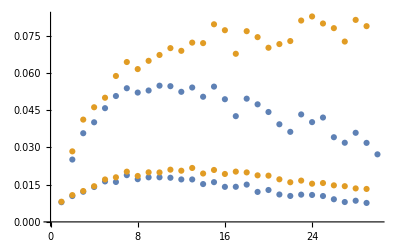

```mathematica
(* COMBINED PR AND RP AVG MSE PLOTS BY WINDOW
-- included data from rf-mse-by-d-chartwall *) 
Show[ListPlot[Transpose@dataPrRmseByD],ListPlot[Transpose@dataRfRmseByD]]
```

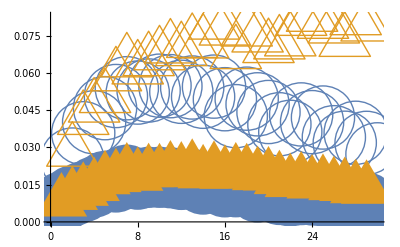

```mathematica
(** PRODUCTION-LEVEL COMBINED IMAGES **) 
(* no legend *)
combinedRmsePlot = Show[ListPlot[Transpose@dataPrRmseByD, PlotMarkers->{Style[◦,Bold,FontSize->65] ,Style[△,Bold,FontSize->61] }],ListPlot[Transpose@dataRfRmseByD,PlotMarkers->{Style[•,Bold,FontSize->63] ,Style[▲,Bold,FontSize->61] }]]
```

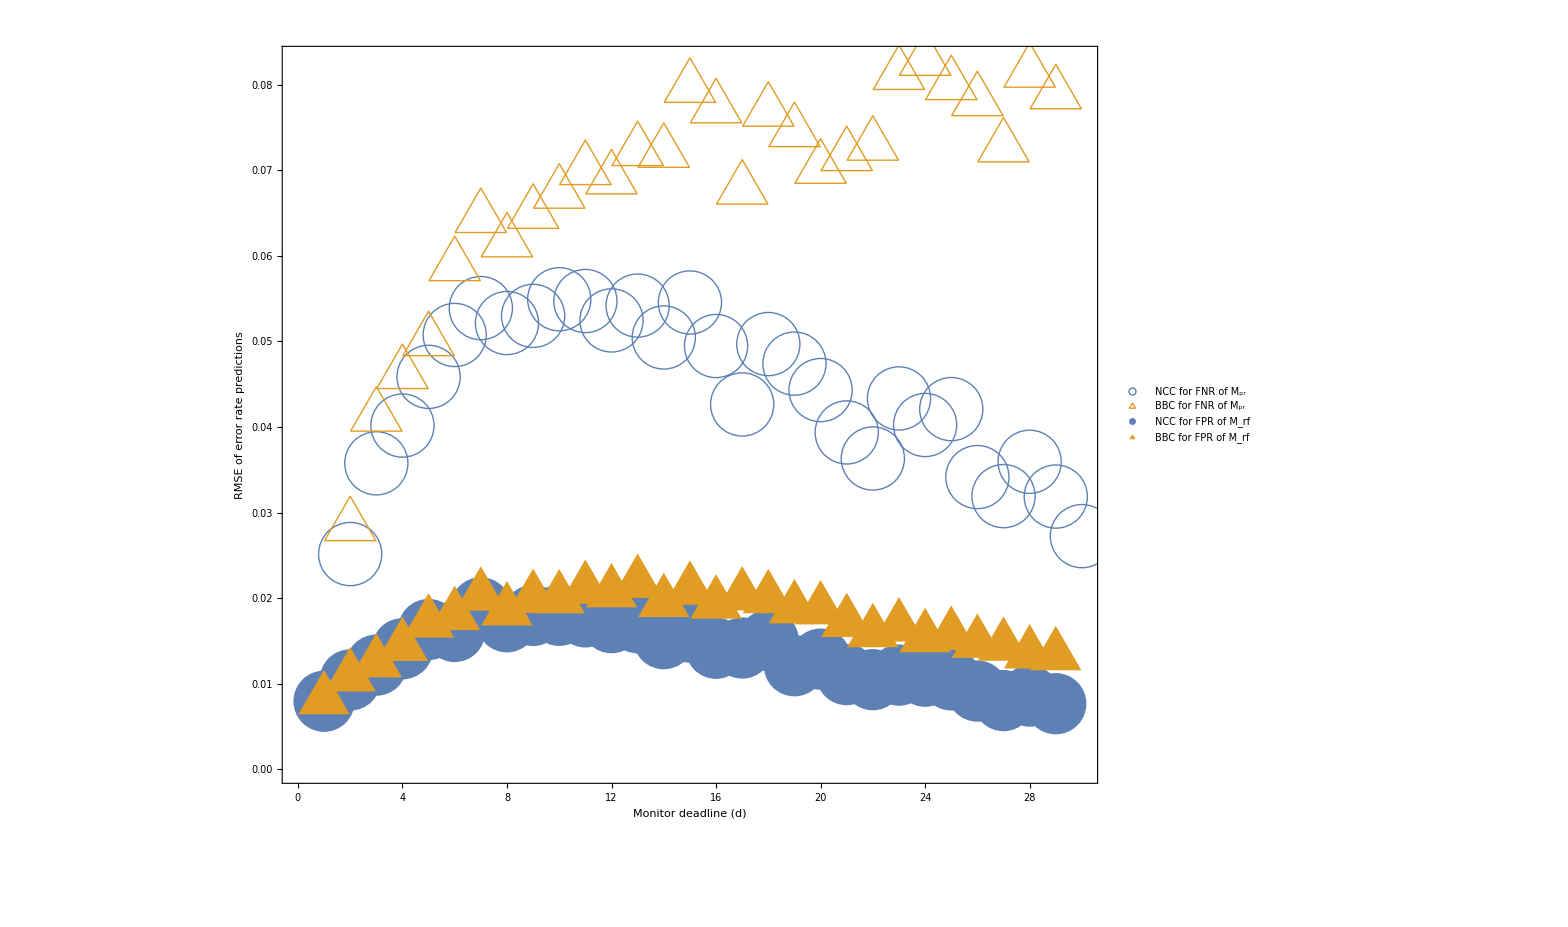

```mathematica
(* with legend *) 
combinedRmsePlotLegended = Legended[Show[combinedRmsePlot, Frame->True, FrameLabel->{StringJoin["Monitor deadline ", ToString[ Style["(d)", Italic], StandardForm]  ],"RMSE of error rate predictions"}, ImageSize->1500, BaseStyle-> {FontSize->35}],Placed[PointLegend[Directive@@@{{ColorData[97,"ColorList"][[1]]} , {ColorData[97,"ColorList"][[2]]},{ColorData[97,"ColorList"][[1]]} ,{ColorData[97,"ColorList"][[2]]} },{StringJoin["NCC for FNR of ",ToString[Subscript[ "M", "pr"], StandardForm]], StringJoin["BBC for FNR of ",ToString[Subscript[ "M", "pr"], StandardForm]],StringJoin["NCC for FPR of ",ToString[Subscript[ "M", "rf"], StandardForm]],StringJoin["BBC for FPR of ",ToString[Subscript[ "M", "rf"], StandardForm]]},
LegendMarkerSize->20,LegendMarkers->{Style[◦,Bold,FontSize->39] , Style[△,Bold,FontSize->33] , Style[•,Bold,FontSize->35] ,Style[▲,Bold,FontSize->33](*Graphics[{Thick,SSSTriangle[1,1,1]}]*)}],{0.15,0.85}]]
```